# Example of tracking graph-theoretic and Entropic properties of a causal network over time

Graph density

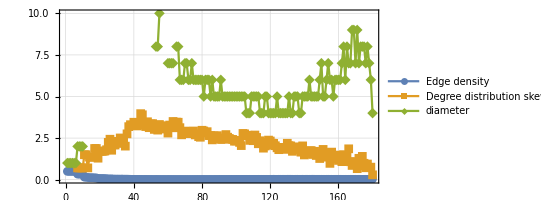

```mathematica
Module[{res=CreateCSSeriesMinkowski[200,3]},ListLinePlot[{(GraphDensity/@AdjacencyGraph/@Last/@res),(Skewness/@VertexDegree/@AdjacencyGraph/@Last/@res),(GraphDiameter/@UndirectedGraph/@AdjacencyGraph/@Last/@res)},PlotLegends->{"Edge\ndensity","Degree\ndistribution\nskewness","diameter"},PlotMarkers->Automatic,Frame->True,AspectRatio->1/2,PlotTheme->"Detailed",PlotStyle->Thick,PlotRange->All,DataRange->All]]
```

Entropy

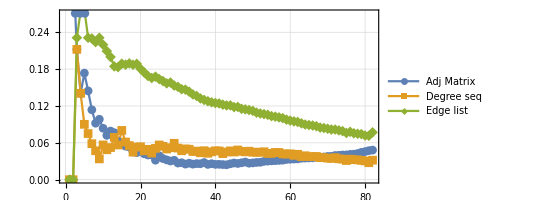

```mathematica
Module[{res=CreateCSSeriesMinkowski[100,3]},ListLinePlot[{(N/@Entropy/@AdjacencyMatrix/@AdjacencyGraph/@Last/@res)/Range[Length[res]],(N/@Entropy/@VertexDegree/@AdjacencyGraph/@Last/@res)/Range[Length[res]],(N/@Entropy/@EdgeList/@AdjacencyGraph/@Last/@res)/Range[Length[res]]},PlotLegends->{"Adj Matrix","Degree seq","Edge list"},PlotMarkers->Automatic,Frame->True,AspectRatio->1/2,PlotTheme->"Detailed",PlotStyle->Thick]]
```

```mathematica
trinetrandomsample=RandomInteger[{0,1645074-1},10000];
```

```mathematica
entropytrinet=Table[N@Entropy@VertexDegree@Last[CreateCSSeriesTrinetReplacement[r,50]],{r,trinetrandomsample}];
```

```mathematica
(10000)/60/60.
```

2.77778

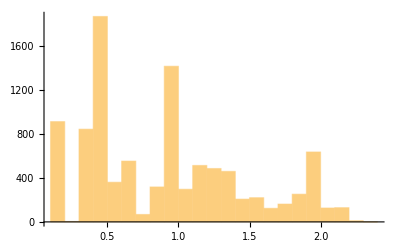

```mathematica
Histogram[entropytrinet]
```

```mathematica
NumberOfTMs[8,2]
```

1208925819614629174706176

```mathematica
tmsample=RandomInteger[{0,1208925819614629174706176-1},10000];
```

```mathematica
Dynamic[r]
```

```mathematica
entropytms=Table[N@Entropy@VertexDegree@AdjacencyGraph[Last@CreateTruningCSTimeSeries[r,8,2,50]],{r,tmsample}];
```

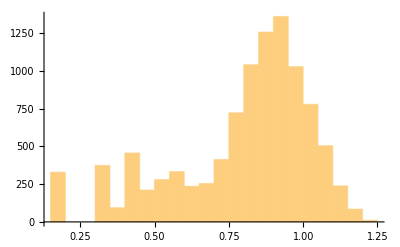

```mathematica
Histogram[entropytms]
```

```mathematica
tmsample2=RandomInteger[{0,NumberOfTMs[7,2]-1},10000];
```

```mathematica
entropytms2=Table[N@Entropy@VertexDegree@AdjacencyGraph[Last@CreateTruningCSTimeSeries[r,7,2,50]],{r,tmsample2}];
```

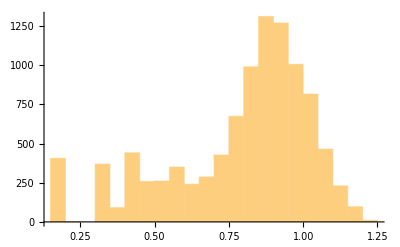

```mathematica
Histogram[entropytms2]
```

```mathematica
tmsample3=RandomInteger[{0,NumberOfTMs[6,2]-1},10000];
```

```mathematica
entropytms3=Table[N@Entropy@VertexDegree@AdjacencyGraph[Last@CreateTruningCSTimeSeries[r,6,2,50]],{r,tmsample3}];
```

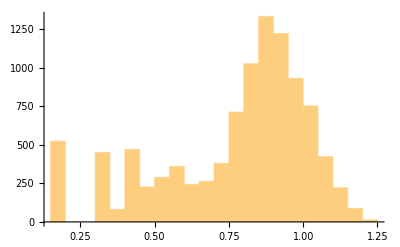

```mathematica
Histogram[entropytms3]
```

```mathematica
tmsample4=RandomInteger[{0,NumberOfTMs[5,2]-1},10000];
```

```mathematica
entropytms4=Table[N@Entropy@VertexDegree@AdjacencyGraph[Last@CreateTruningCSTimeSeries[r,5,2,50]],{r,tmsample4}];
```

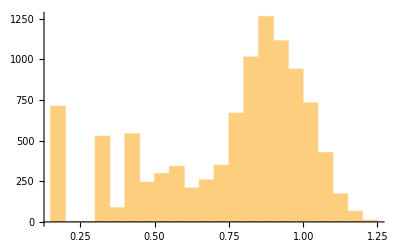

```mathematica
Histogram[entropytms4]
```

Information flow

```mathematica
FindMaximumFlow[Graph[List["s",1,2,3,4,5,6,"t"],List[DirectedEdge["s",1],DirectedEdge["s",2],DirectedEdge["s",3],DirectedEdge[1,4],DirectedEdge[2,5],DirectedEdge[3,6],DirectedEdge[4,"t"],DirectedEdge[5,"t"],DirectedEdge[6,"t"],DirectedEdge[3,5],DirectedEdge[2,4]]], "s", "t", "OptimumFlowData"]
```

OptimumFlowData[<8>, <9>]

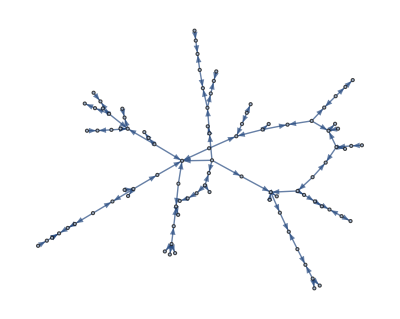
FindMaximumFlow[-Graphics-,s,t,OptimumFlowData]

```mathematica
FindMaximumFlow[dag, "s", "t", "OptimumFlowData"]
```

```mathematica
ℱ = FindMaximumFlow[-Graphics-, "s", "t", "OptimumFlowData"];
```

```mathematica
ℱ["FlowValue"]
```

0.3[FlowValue]

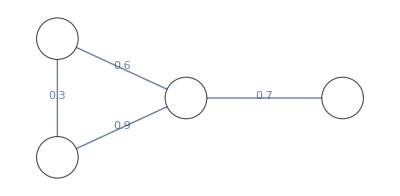
```mathematica
ℱ = FindMaximumFlow[-Graphics-, 1,4, "OptimumFlowData"]
```

OptimumFlowData[<4>, <3>]

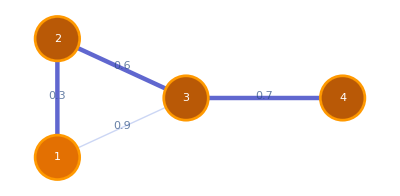

```mathematica
ℱ["FlowGraph"]
```

```mathematica
N@Entropy@VertexDegree[Last@CreateCSSeriesTrinetReplacement[2345,20]]
```

0.775129

```mathematica
Dynamic[m]
```

```mathematica
1645074/1000./60
```

27.4179

```mathematica
rsample=RandomInteger[{0,1645074-1},1000];
```

```mathematica
degentvalues=Table[N@Entropy@VertexDegree[Last@CreateCSSeriesTrinetReplacement[m,10]],{m,2345}];
```

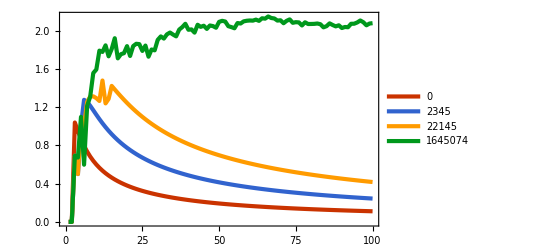

```mathematica
ListLinePlot[{N/@Entropy/@VertexDegree/@CreateCSSeriesTrinetReplacement[0,100],N/@Entropy/@VertexDegree/@CreateCSSeriesTrinetReplacement[2345,100],N/@Entropy/@VertexDegree/@CreateCSSeriesTrinetReplacement[22145,100],N/@Entropy/@VertexDegree/@CreateCSSeriesTrinetReplacement[1645074,100]},PlotStyle->Thick,Frame->True,PlotTheme->"Web",PlotLegends->{0,2345,22145,1645074}]
```

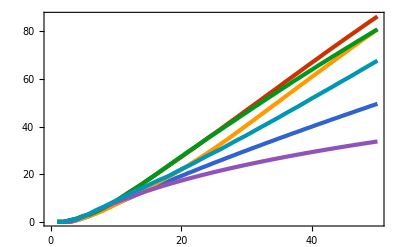

```mathematica
ListLinePlot[Accumulate/@Table[N/@Entropy/@VertexDegree/@CreateCSSeriesTrinetReplacement[1645074-i,50],{i,RandomInteger[{1,100},6]}],PlotTheme->"Web",Frame->True]
```

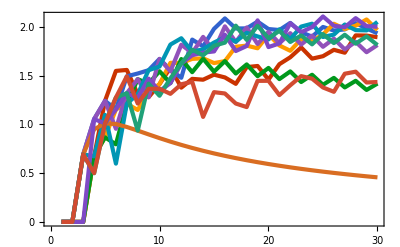

```mathematica
ListLinePlot[Table[N/@Entropy/@VertexDegree/@CreateCSSeriesTrinetReplacement[1645074-i,30],{i,RandomInteger[{1,100},10]}],PlotTheme->"Web",Frame->True]
```

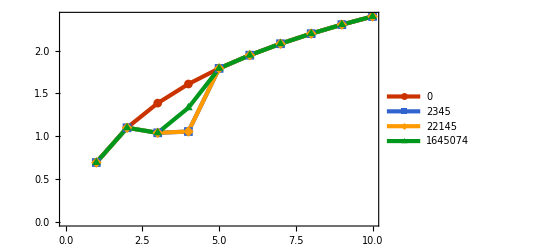

```mathematica
ListLinePlot[{N/@Entropy/@Normal/@(AdjacencyMatrix/@CreateCSSeriesTrinetReplacement[0,10]),N/@Entropy/@Normal/@(AdjacencyMatrix/@CreateCSSeriesTrinetReplacement[2345,10]),N/@Entropy/@Normal/@(AdjacencyMatrix/@CreateCSSeriesTrinetReplacement[22145,10]),N/@Entropy/@Normal/@(AdjacencyMatrix/@CreateCSSeriesTrinetReplacement[1645074,10])},PlotStyle->Thick,Frame->True,PlotTheme->"Web",PlotLegends->{0,2345,22145,1645074},PlotMarkers->Automatic]
```

```mathematica
degentvalues2=Table[N@Entropy@VertexDegree[Last@CreateCSSeriesTrinetReplacement[m,20]],{m,rsample}];
```

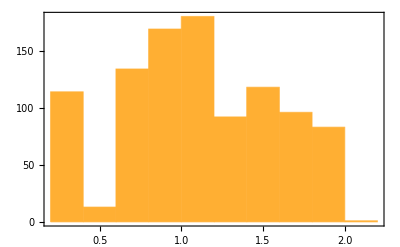

```mathematica
Histogram[degentvalues2,N@Log[2],PlotTheme->"Web",Frame->True]
```

```mathematica
SortBy[Thread[{rsample,degentvalues2}],Last][[-1]]
```

{1289160,2.00448}

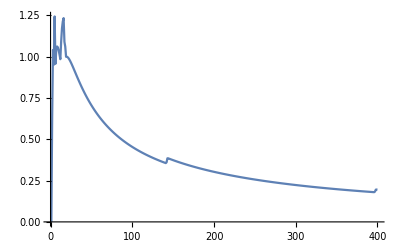

```mathematica
ListLinePlot[N/@Entropy/@VertexDegree/@AdjacencyGraph/@CreateTruningCSTimeSeries[378,2,2,400]]
```

```mathematica
ListLinePlot[N/@Entropy/@VertexDegree/@AdjacencyGraph/@CreateTruningCSTimeSeries[378,2,2,400]]
```

```mathematica
NumberOfTMs[s_,k_]:=(2 s k)^(s k)
```

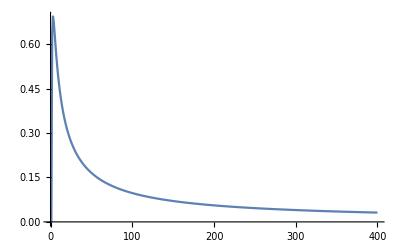

```mathematica
ListLinePlot[N/@Entropy/@VertexDegree/@AdjacencyGraph/@CreateTruningCSTimeSeries[4096-1,2,2,400],PlotRange->All]
```

```mathematica
randTMs=RandomInteger[{0,4096-1},20];
```

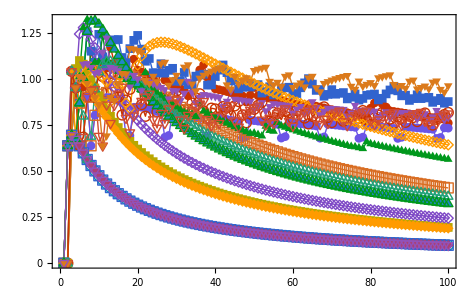

```mathematica
ListLinePlot[Table[N/@Entropy/@VertexDegree/@AdjacencyGraph/@CreateTruningCSTimeSeries[m,2,2,100],{m,randTMs}],PlotStyle->Thick,Frame->True,PlotTheme->"Web",PlotMarkers->Automatic]
```

```mathematica
NumberOfTMs[8,2]
```

1208925819614629174706176

```mathematica
randTMs2=RandomInteger[{0,1208925819614629174706176-1},50];
```

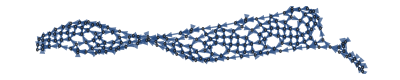
```mathematica
ShellDimension[-Graphics-]
```

3

```mathematica
Median/@VertexDegree/@Table[AdjacencyGraph[Last@CreateTruningCSTimeSeries[m,8,2,200]],{m,randTMs2}]
```

{4,4,3,4,3,3,3,3,3,3,4,4,3,4,4,3,3,3,3,4,3,4,4,4,4,3,3,4,3,3,3,3,4,4,2,4,3,3,4,2,3,3,3,3,4,4,3,3,3,3}

```mathematica
VertexDegree@AdjacencyGraph[Last@CreateTruningCSTimeSeries[randTMs2[[3]],8,2,30]]
```

{2,3,3,2,3,4,4,3,4,3,3,4,3,3,4,3,3,3,2,2,2,3,3,3,4,3,3,3,2,2,1}